```mathematica
data = Import["/Users/ashepelev/astro/astro.notebook/astro.notebook.third/data/gr.txt","Table"];
```

```mathematica
plot = Table[{data[[i,2]] - data[[i,3]], -(data[[i,2]]+5+5Log10[data[[i,4]]/1000])},{i,2,Length@data}]
```

{{0.507,-4.15282},{0.435,-3.35525},{0.523,-4.53818},{0.537,-4.44164},{0.677,-4.9151},{0.465,-3.04206},39226,{0.53,3.71899},{0.52,2.56545},{0.23,2.70937},{0.68,0.6006},{0.68,1.28666}}
 |  |  |  |

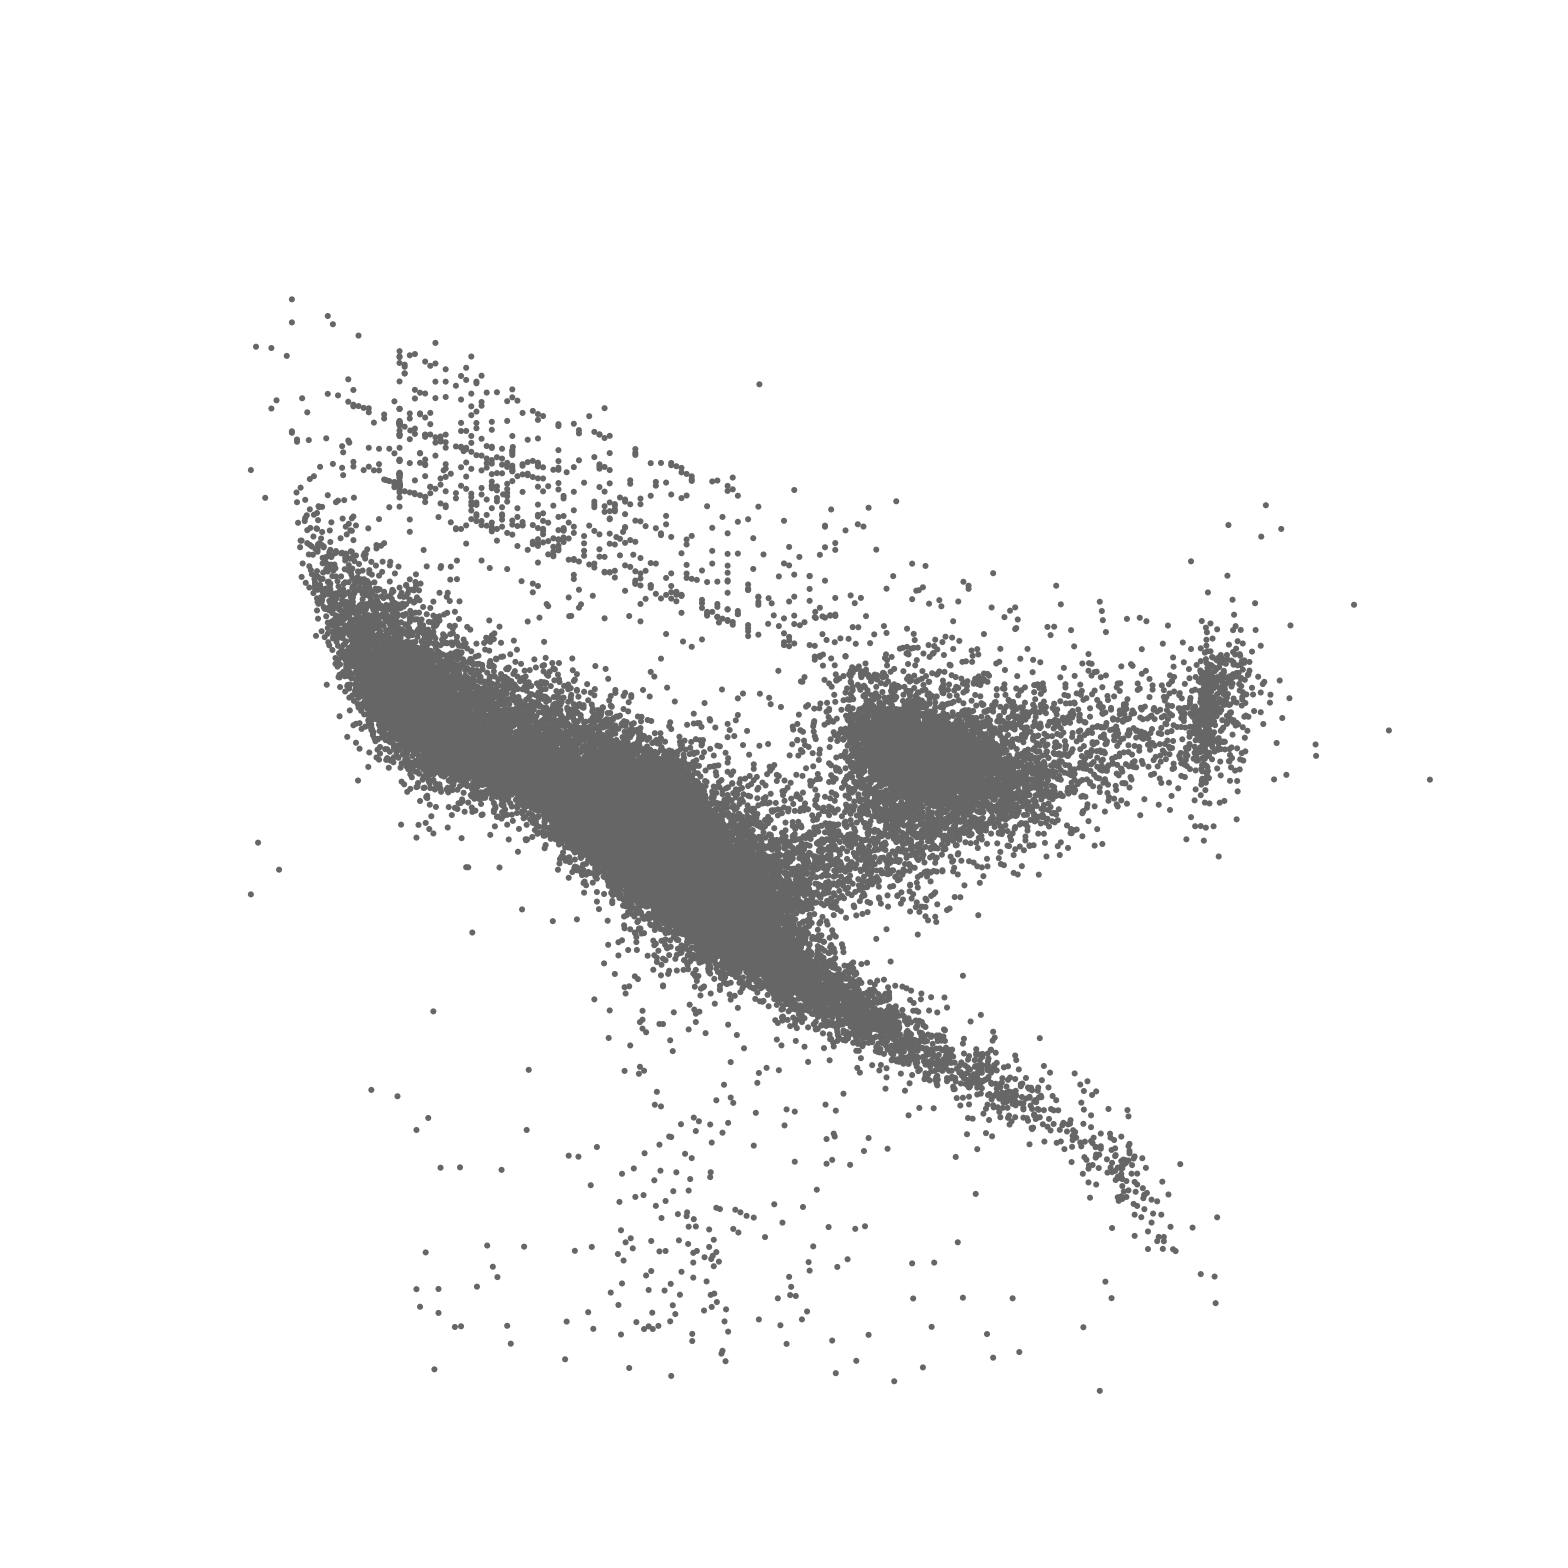

```mathematica
ListPlot[plot, AspectRatio->5/4,PlotRange->{{-0.5, 2},{-15,10}}, ImageSize->2000,PlotStyle->RGBColor[0.4,0.4,0.4], Axes->None]
```

```mathematica
tmp=Join[{{"BV","M"}},RandomSample[Table[{SetPrecision[plot[[i,1]],4],SetPrecision[-plot[[i,2]],4]},{i,1,Length@plot}], Round[Length@plot/5.7]]]
```

{{BV,M},{0.336,2.395},{0.6,5.12},{0.042,1.606},{0.928,1.423},6875,{0.645,4.752},{0.759,5.731},{0.392,2.343},{0.621,4.56},{0.611,4.265}}
 |  |  |  |

```mathematica
Export["/Users/ashepelev/astro/astro.notebook/astro.notebook.third/data/gr-plot.txt",tmp, "Table"]
```

/Users/ashepelev/astro/astro.notebook/astro.notebook.third/data/gr-plot.txt